```mathematica
(*Problema 1:*)
f[x_]:=x E^x-1
```

```mathematica
(*Única solución:*)
f'[x]
```

ⅇ^x+ⅇ^x x

```mathematica
(*La derivada se anual en x=-1*)
Solve[f'[x]==0]
```

{{x→-1}}

```mathematica
(*Intervalos de monotonía (-Infinity,-1), (-1,+Infinity). EStudiar cambio de signo en cada uno:*)
Limit[f[x],x->-Infinity]
f[-1.]
Limit[f[x],x->+Infinity]
```

-1

-1.36788

∞

```mathematica
(*Solo hay cambio de signo en (-1,+Infinity). Por tanto, este es el intervalo que contiene soluciñón y es única. El otro no presenta cambio de signo y no tiene solución.

Acabamos de demostrar que la solución es única y que está en (-1,+Infinity)*)
x0=0.`20
g[x_]:=x-f[x]/f'[x]
```

0.

```mathematica
x1=g[x0]
ea=Abs[x1-x0]
ea<10^-5
```

1.

1.

False

```mathematica
x1=1.`20
```

1.

```mathematica
x2=g[x1]
ea=Abs[x2-x1]
ea<10^-5
```

0.6839397205857211608

0.316060279414278839

False

```mathematica
x3=g[x2]
ea=Abs[x3-x2]
ea<10^-5
```

0.577454477154449716

0.106485243431271445

False

```mathematica
x4=g[x3]
ea=Abs[x4-x3]
ea<10^-5
```

0.567229737730117042

0.01022473942433267

False

```mathematica
x5=g[x4]
ea=Abs[x5-x4]
ea<10^-5
```

0.567143296530295929

0.000086441199821113

False

```mathematica
x6=g[x5]
ea=Abs[x6-x5]
ea<10^-5
```

0.5671432904097839

6.12051203×10^-9

True

```mathematica
(*Con precisión*)
x2=g[x1]
ea=Abs[x2-x1]/Abs[x2]
ea<10^-5
```

0.6839397205857211608

0.462117157260009759

False

```mathematica
x3=g[x2]
ea=Abs[x3-x2]/Abs[x3]
ea<10^-5
```

0.577454477154449716

0.184404568055310465

False

```mathematica
x4=g[x3]
ea=Abs[x4-x3]/Abs[x4]
ea<10^-5
```

0.567229737730117042

0.01802574643785251

False

```mathematica
x5=g[x4]
ea=Abs[x5-x4]/Abs[x5]
ea<10^-5
```

0.567143296530295929

0.00015241509570852

False

```mathematica
x6=g[x5]
ea=Abs[x6-x5]/Abs[x6]
ea<10^-5
```

0.5671432904097839

1.07918266×10^-8

True

```mathematica
(*Asegurar convergencia: empíricamente....

Regla de Fourier:
1) f es de clase infnito
2) Existe un única solución en el intervalo (-1,+Infinito) y en cualquier contenido en él con cambio de signo. Por ejemplo: [0,1]*)
f[0]
f[1.]
```

-1

1.71828

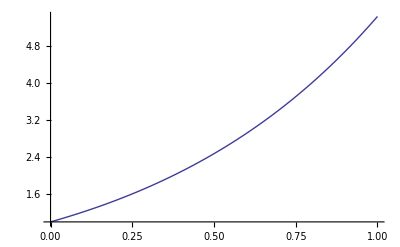

```mathematica
(*3) La función f' no se anula en ese intervalo:*)
Plot[f'[x],{x,0,1}]
```

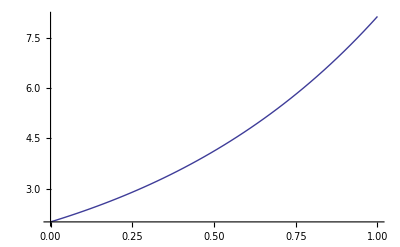

```mathematica
(*4) La derivada segunda f'' no se anula en ese interval*)
Plot[f''[x],{x,0,1}]
```

```mathematica
(*5) Mismo signo de f y f'' en extremos:*)
f[0]*f''[0]
f[1.]*f''[1]
```

-2

14.0123

```mathematica
(*Por tanto x0=1. Pero como el iterado que genera x0=0 es precisamente x1=1 y para este la convergencia está asegurada, pues entonces la convergencia está asegurada para x0=0.*)
```

```mathematica
(*Problema 2*)
f[x_]:=(x^3-2x^2+x)-(2x^2+3x+1)
```

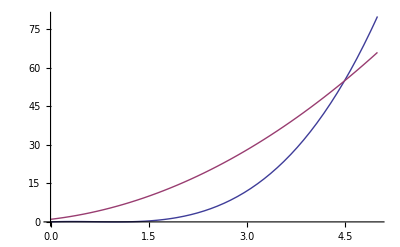

```mathematica
Plot[{x^3-2x^2+x,2x^2+3x+1},{x,0,5}]
```

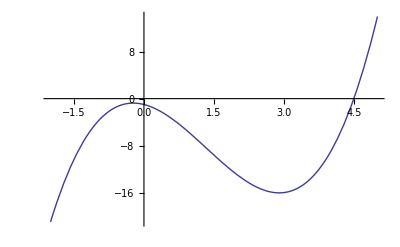

```mathematica
Plot[f[x],{x,-2,5}]
```

```mathematica
(*Comprobar que se cortan en un único punto:*)
f'[x]
```

-2-8 x+3 x^2

```mathematica
Solve[f'[x]==0]
```

{{x→1/3 (4-√22)},{x→1/3 (4+√22)}}

```mathematica
(*Tres intervalos de monotonía:*)
Limit[f[x],x->-Infinity]
f[1/3 (4-√22.)]
f[1/3 (4+√22.)]
Limit[f[x],x->Infinity]
```

-∞

-0.763767

-16.051

∞

```mathematica
(*El único cambio de signo es en el último intervalo. HAgámoslo más pequeño*)
1/3 (4+√22.)
```

2.89681

```mathematica
f[3]
f[4]
f[5]
f[6]
f[7]
```

-16

-9

14

59

132

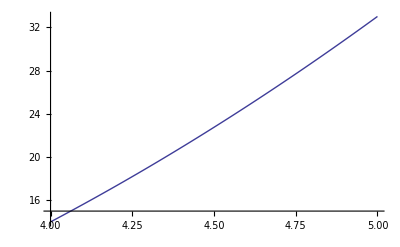

```mathematica
(*El cambio de signo es en el intervalo [4,5] y es donde está la única solución*)


(*Regla de FOurier:
1) f es de clase infinito
2) La solución es única en [4,5]
3) La derivada primera no se anula en [4,5]*)
Plot[f'[x],{x,4,5}]
```

```mathematica
f'[4]
```

14

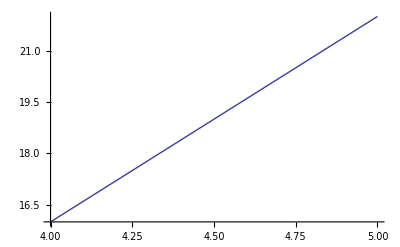

```mathematica
(*4) La derivada segunda f'' no se anula en [4,5]*)
Plot[f''[x],{x,4,5}]
```

```mathematica
(*5) Mismo signo de f y f'' en los extremos:*)
f[4]*f''[4]
f[5]*f''[5]
```

-144

308

```mathematica
(*Se coge x0=5*)
x0=5`20
g[x_]:=x-f[x]/f'[x]
```

5.

```mathematica
x1=g[x0]
ea=Abs[(x1-x0)/x1]
ea<5*10^-5
```

4.575757575757575758

0.0927152317880794702

False

```mathematica
x2=g[x1]
ea=Abs[(x2-x1)/x2]
ea<5*10^-5
```

4.49712442508618678

0.01748520682077459

False

```mathematica
x3=g[x2]
ea=Abs[(x3-x2)/x3]
ea<5*10^-5
```

4.4944957324436174

0.00058486931550387

False

```mathematica
x4=g[x3]
ea=Abs[(x4-x3)/x4]
ea<5*10^-5
```

4.4944928370589284

6.442072096×10^-7

True

```mathematica
(*La convergencia es cuadrática por ser de clase infinto y no anularse la derivada*)
```

```mathematica
(*Problema 3:*)
f[x_]:=25 x+10x^2-10x^3-x^4+x^5-25
```

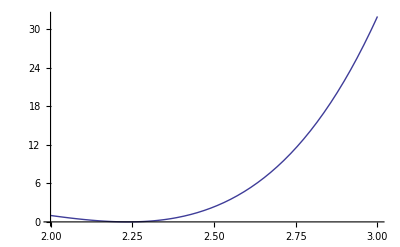

```mathematica
Plot[f[x],{x,2,3}]
```

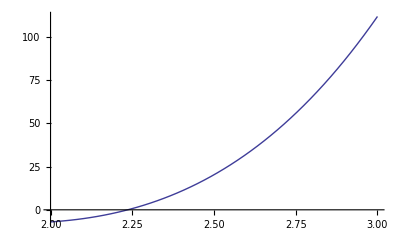

```mathematica
Plot[f'[x],{x,2,3}]
```

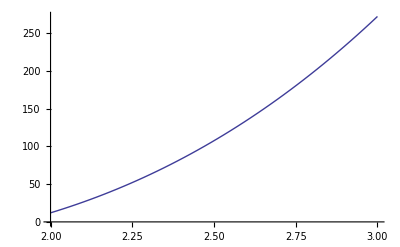

```mathematica
Plot[f''[x],{x,2,3}]
```

```mathematica
f[2]*f''[2]
```

12

```mathematica
f[3]*f''[3]
```

8704

```mathematica
Solve[f[x]==0]
```

{{x→1},{x→-√5},{x→-√5},{x→√5},{x→√5}}

```mathematica
Solve[f'[x]==0]
```

{{x→-√5},{x→√5},{x→1/5 (2-√29)},{x→1/5 (2+√29)}}

```mathematica
(*Podemos coger cualquiera de ellos*)
```

```mathematica
x0:=2.`20
g[x_]:=x-f[x]/f'[x]
```

```mathematica
x1=g[x0]
f'[x1]
ea=Abs[(x1-x0)/x1]
ea<5*10^-5
```

2.14285714285714286

-3.83173677634319

0.066666666666666667

False

```mathematica
x2=g[x1]
f'[x2]
ea=Abs[(x2-x1)/x2]
ea<5*10^-5
```

2.192546583850932

-1.978685888538

0.022662889518414

False

```mathematica
x3=g[x2]
f'[x3]
ea=Abs[(x3-x2)/x3]
ea<5*10^-5
```

2.2149358496111

-1.0036077757

0.0101083134142

False

```mathematica
x4=g[x3]
f'[x4]
ea=Abs[(x4-x3)/x4]
ea<5*10^-5
```

2.2256459052

-0.50522185

0.00481211121

False

```mathematica
x5=g[x4]
f'[x5]
ea=Abs[(x5-x4)/x5]
ea<5*10^-5
```

2.2308915

-0.25345

0.0023513

False

```mathematica
(*Perdemos mucha precisión y vamos muy lento... Como puede verse la derivada primera cada vez se hace más cercana a cero... Y la gráfica lo corrobora. Procedamos con el método modificado*)
```

```mathematica
x0:=2.`20
g[x_]:=x-2*f[x]/f'[x]
```

```mathematica
x1=g[x0]
f'[x1]
ea=Abs[(x1-x0)/x1]
ea<5*10^-5
```

2.28571428571428571

2.68929612661391

0.125

False

```mathematica
x2=g[x1]
f'[x2]
ea=Abs[(x2-x1)/x2]
ea<5*10^-5
```

2.23752737892431

0.072355333646

0.02153578420709

False

```mathematica
x3=g[x2]
f'[x3]
ea=Abs[(x3-x2)/x3]
ea<5*10^-5
```

2.2360693129

0.00006603

0.00065206656

False

```mathematica
x4=g[x3]
f'[x4]
ea=Abs[(x4-x3)/x4]
ea<5*10^-5
```

2.236

0.

0.

True

```mathematica
(*Meter más precisión: 30*)
```

```mathematica
(*Problema 4*)
a:={{1,1.51`3,0,4.52`3},{0,-3,0.5`3,-6.61`3},{2,-2,1,0.85`3}}
```

```mathematica
MatrixForm[a]
```

(1 | 1.51 | 0 | 4.52
0 | -3 | 0.5 | -6.61
2 | -2 | 1 | 0.85)

```mathematica
(*Pivoteo parcial: Los candidatos en la primera columna son 1, 0 y 2. POr tanto, gana el 2 y debemos seleccionar ese como pivote. Intercambiamos fila 1 y 3*)
f=a[[1]]
a1=ReplacePart[a,a[[3]],1]
a1=ReplacePart[a1,f,3]
MatrixForm[a1]
```

{1,1.51,0,4.52}

{{2,-2,1,0.85},{0,-3,0.5,-6.61},{2,-2,1,0.85}}

{{2,-2,1,0.85},{0,-3,0.5,-6.61},{1,1.51,0,4.52}}

(2 | -2 | 1 | 0.85
0 | -3 | 0.5 | -6.61
1 | 1.51 | 0 | 4.52)

```mathematica
(*Pivotamos*)
a2=ReplacePart[a1,a1[[3]]-a1[[3,1]]*a1[[1]]/a1[[1,1]],3]
MatrixForm[a2]
```

{{2,-2,1,0.85},{0,-3,0.5,-6.61},{0,2.51,-1/2,4.1}}

(2 | -2 | 1 | 0.85
0 | -3 | 0.5 | -6.61
0 | 2.51 | -1/2 | 4.1)

```mathematica
(*Pivotamos la columna 2: Los candidatos son 3 y 2.51. Gana 3 y no se modifica el sistema*)
a3G=ReplacePart[a2,a2[[3]]-a2[[3,2]]*a2[[2]]/a2[[2,2]],3]
MatrixForm[a3G]
```

{{2,-2,1,0.85},{0,-3,0.5,-6.61},{0,0.,-0.082,-1.4}}

(2 | -2 | 1 | 0.85
0 | -3 | 0.5 | -6.61
0 | 0. | -0.082 | -1.4)

```mathematica
a3GJ=ReplacePart[a3G,a2[[1]]-a2[[1,2]]*a2[[2]]/a2[[2,2]],1]
MatrixForm[a3GJ]
```

{{2,0,0.667,5.26},{0,-3,0.5,-6.61},{0,0.,-0.082,-1.4}}

(2 | 0 | 0.667 | 5.26
0 | -3 | 0.5 | -6.61
0 | 0. | -0.082 | -1.4)

```mathematica
(*Pivotamos columna 3 solo en GJ, porque en G no tiene sentido:*)
a4GJ=ReplacePart[a3GJ,a3GJ[[1]]-a3GJ[[1,3]]*a3GJ[[3]]/a3GJ[[3,3]],1]
a4GJ=ReplacePart[a4GJ,a3GJ[[2]]-a3GJ[[2,3]]*a3GJ[[3]]/a3GJ[[3,3]],2]
MatrixForm[a4GJ]
```

{{2,0.,0.,-6.},{0,-3,0.5,-6.61},{0,0.,-0.082,-1.4}}

{{2,0.,0.,-6.},{0,-3.,0.,-20.},{0,0.,-0.082,-1.4}}

(2 | 0. | 0. | -6.
0 | -3. | 0. | -20.
0 | 0. | -0.082 | -1.4)

```mathematica
(*RESOLUCION GAUSS:*)
a3G//MatrixForm
```

(2 | -2 | 1 | 0.85
0 | -3 | 0.5 | -6.61
0 | 0. | -0.082 | -1.4)

```mathematica
z=a3G[[3,4]]/a3G[[3,3]]
y=(a3G[[2,4]]-a3G[[2,3]]*z)/a3G[[2,2]]
x=(a3G[[1,4]]-a3G[[1,3]]*z-a3G[[1,2]]*y)/a3G[[1,1]]
```

20.

5.

-3.

```mathematica
(*RESOLUCIÓN GAUSS-JORDAN:*)
a4GJ//MatrixForm
```

(2 | 0. | 0. | -6.
0 | -3. | 0. | -20.
0 | 0. | -0.082 | -1.4)

```mathematica
z=a4GJ[[3,4]]/a4GJ[[3,3]]
y=a4GJ[[2,4]]/a4GJ[[2,2]]
x=a4GJ[[1,4]]/a4GJ[[1,1]]
```

20.

5.

-3.

```mathematica
(*Pivoteo Parcial escalado: Primero los si:*)
a//MatrixForm
```

(1 | 1.51 | 0 | 4.52
0 | -3 | 0.5 | -6.61
2 | -2 | 1 | 0.85)

```mathematica
s1=a[[1,2]]
s2=Abs[a[[2,2]]]
s3=a[[3,1]]
```

1.51

3

2

```mathematica
(*Ver el pivote*)
a[[1,1]]/s1
a[[2,1]]/s2
a[[3,1]]/s3
```

0.662

0

1

```mathematica
(*Vuelve a ser el mismo pivote y por tanto la misma matriz:*)
a1//MatrixForm
```

(2 | -2 | 1 | 0.85
0 | -3 | 0.5 | -6.61
1 | 1.51 | 0 | 4.52)

```mathematica
a2//MatrixForm
```

(2 | -2 | 1 | 0.85
0 | -3 | 0.5 | -6.61
0 | 2.51 | -1/2 | 4.1)

```mathematica
(*Pivotamos la columna 2:*)

(*Recuerda que para obtener la matriz anterior, tuvimos que intercambiar las filas 1 y 3, por lo que debemos también intercambiar los factores de escala de esas dos filas. Puedes hacerlo de dos maneras, bien teniendo en cuenta que ahora el factor de escala de la fila 1 es s3 y el de la fila 2 es s1, que suele ser lo más cómodo y haríamos el cálculo siguiente:*)
Abs[a2[[2,2]]]/s2
a2[[3,2]]/s1
```

1

1.7

```mathematica
(*En este caso, debemos intercambiar las filas 2 y 3.*)

(*De manera alternativa, podemos hacer un intercambio de los valores de s1 y s3 de modo que podamos seguir usando s3 para la fila 3 y s1 para la fila 1... Simplemente hay que intercambiar los valores:*)
f=s3
s3=s1
s1=f
```

2

1.51

2

```mathematica
(*Y ya se calculan los pivotes escalados:*)
Abs[a2[[2,2]]]/s2
a2[[3,2]]/s3
```

1

1.7

```mathematica
(*Obviamente salen los mismos resultados*)
```